# Cooking a Spherical Chicken!

By Gianmarco Morbelli

University of Groningen

You studied in class the thermal diffusion equation (or simply the heat equation). It is best now to apply it to some practical examples: we will investigate the behaviour of the temperature of a spherical chicken inside an oven! 
Let’s first sketch the situation:

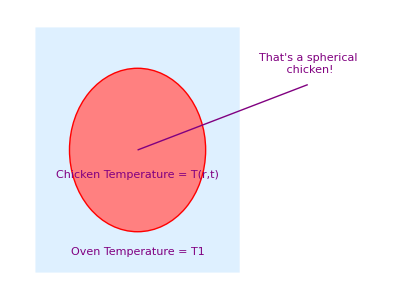

```mathematica
Graphics[{Thick,LightBlue,Rectangle[{-1,-1},{2,2}],Pink,Disk[{0.5,0.5}],Red,Circle[{0.5,0.5}],Purple,Arrowheads[Large],Arrow[{{3,1.3},{0.5,0.5},{0.5,0.5}}], Text["That's a spherical
 chicken!",{3,1.55}],Purple,Arrowheads[Large],Text["Oven Temperature = T1",{0.5,-0.75}],Text["Chicken Temperature = T(r,t)",{0.5,0.2}] }]
```

## Analytical solution

We will propose two simulations: one analytical and one numerical.

Recall the heat equation (without heat source term) is given by:

where  is the thermal diffusivity. A quick Google search gives a mean value of    of approximately

```mathematica
0.4930/3654*896.07
```

0.120898

In our case the problem is nicely spherical symmetric, as it is physically reasonable to assume that the temperature distribution inside the chicken will depend only on the radial coordinate from the center. As shown in the book, the heat equation can be simplified to one dimension by applying the change of variable:

which yields

with the appropriate boundary and initial conditions:

where  is the original temperature of the chicken and  the temperature of the oven (which we assume fixed).

We now set up the code to solve the partial differential equation using DSolve which, in this case, is able to solve the problem analytically:

```mathematica
Tchickeninit=T0;
Toven=T1;
```

```mathematica
boundaryconditions={b[0,t]==0,b[a,t]==0,b[r,0]==r(T0-T1)};
```

```mathematica
heatequation=D[b[r,t],t]==d D[b[r,t],{r,2}];
```

```mathematica
solution[r_]:=DSolveValue[{heatequation,boundaryconditions},b[r,t],{r,t}]
```

We solved for the , but the we are actually interested in the physical temperature  (the next line may take some time to evaluate):

```mathematica
temperature[r_]=T1+solution[r]/r
```

T1+(-(2 (-1)^K[1] a ⅇ^(-(d π^2 t K[1]^2)/a^2) (T0-T1) Sin[(π r K[1])/a])/(π K[1])K[1]1∞)/r

In order to plot it, we select the first few terms of the infinite sum:

```mathematica
approxsol[r_]:=temperature[r]/. {Infinity->5}//Activate//Expand;
Manipulate[Block[{d=0.12,T0=300,T1=500,a},
SliceDensityPlot3D[Evaluate[approxsol[√(x^2+y^2+z^2)]/.{t->time,a->radius}],"CenterCutSphere",{x,y,z} ∈Ball[{0,0,0},radius+5],PlotRange->Full,ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{300,500},{0,1}]]&),PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Text["Temperature in Kelvins"]],{After,Top}],PlotLabel->Style[Join[Framed["Temperature at the center = "<>ToString[approxsol[0.1]/.{t->time,a->radius}]<>" K"]],16,Black,Background->Lighter[Pink]]]],{{time, 0.1, "Time (s)"},0.1,50,1,Appearance->"Labeled"},{{radius,5,"Radius"},1,10,1,Appearance->"Labeled"}]
```

## Numerical solution

We can also solve numerically using NDSolve for a faster visualization:

```mathematica
boundaryconditions2={B[0,t]==0,B[a,t]==0};
initialconditions2={B[r,0]==UnitStep[a-r-0.00001]*r(T0-T1)};
```

```mathematica
heateq2=D[B[r,t],t]==κ D[B[r,t],{r,2}];
```

```mathematica
Manipulate[Block[{solution2=Block[{κ=0.12,T0=300,T1=500,a=radius},NDSolve[{heateq2,boundaryconditions2,initialconditions2},B[r,t],{t,0,1000},{r,0,radius}]]},Block[{T1=500},SliceDensityPlot3D[Evaluate@First[T1+(B[r,t]/r)/.solution2/.{r->√(x^2+y^2+z^2),t->i}],"CenterCutSphere",{x,y,z}∈Ball[{0,0,0},radius],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{280,500},{0,1}]]&),PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Text["Temperature in Kelvins"]],{After,Top}],PlotLabel->Style[Join[Framed["Temperature at the center = "<>ToString[Evaluate@First[T1+(B[r,t]/r)/.solution2/.{r->0.01,t->i}]]<>" K"]],16,Black,Background->Lighter[Pink]]]]],{{i,0,"Time (s)"},0,100,1,Appearance->"Labeled"},{{radius,5,"Radius"},1,10,1,Appearance->"Labeled"}]
```